```mathematica
Quit[]
```

# Neutral Current Drell-Yan

Here is presented the evaluation of the master integrals that appear in the calculations for the mixed EW-QCD corrections to the neutral current Drell-Yan. For a more comprehensive discussion see: https://arxiv.org/abs/2201.01754

### Import the package and the system of differential equations

```mathematica
SetDirectory[NotebookDirectory[]];
<<"../SeaSyde.m"
```

+++++ SeaSyde` +++++
Version 1.1.0

SeaSyde is a package for solving the system of differential equation associated to the Master Integrals of a given topology.

For any question or comment, please contact: 
[T. Armadillo](mailto:tommaso.armadillo@uclouvain.be), [R. Bonciani](mailto:roberto.bonciani@roma1.infn.it), [S. Devoto](mailto:simone.devoto@unimi.it), [N. Rana](mailto:narayan.rana@unimi.it) or [A. Vicini](mailto:alessandro.vicini@mi.infn.it).

For the latest version please see the [GitHub repository](https://github.com/TommasoArmadillo/SeaSyde).

```mathematica
dir="EquationsAndBC/NeutralCurrentDrellYan/";

EquationX=ReadFrom[dir<>"equations_x.m"];
EquationY=ReadFrom[dir<>"equations_y.m"];
FullSystemOfEquations=Join[EquationX,EquationY];

MasterIntegrals=Table[Subscript[B, i][x,y],{i,1,36}];

AsymptoticBoundaryConditions=ReadFrom[dir<>"bc_asymptotic.m"];
PointBC={0,1};
```

SeaSyde: File EquationsAndBC/NeutralCurrentDrellYan/equations_x.m has been correctly read.

SeaSyde: File EquationsAndBC/NeutralCurrentDrellYan/equations_y.m has been correctly read.

SeaSyde: File EquationsAndBC/NeutralCurrentDrellYan/bc_asymptotic.m has been correctly read.

The system of differential equations is in a form such that the simplest equation is in first place. It must always be this way. The boundary conditions are given in the limit x->0+, y=1.

### Configure and setup the package

```mathematica
ConfigurationDrellYan={
EpsilonOrder->4,
ExpansionOrder->50,
LogarithmicSingularities ->{{0,-1,-(4 y^2)/(1+y)^2,-y,-4},{0}},
SafeSingularities -> {{-(4 (-1+y))/y},{1,4/(4+x),-x,(-2 √-x-x)/(4+x),(2 √-x-x)/(4+x)}}
};
UpdateConfiguration[ConfigurationDrellYan]
```

SeaSyde: Updated EpsilonOrder parameter, new value -> 4

SeaSyde: Updated ExpansionOrder parameter, new value -> 50

SeaSyde: Updated LogarithmicSingularities parameter, new value -> {{0,-1,-(4 y^2)/(1+y)^2,-y,-4},{0}}

SeaSyde: Updated SafeSingularities parameter, new value -> {{-(4 (-1+y))/y},{1,4/(4+x),-x,(-2 √-x-x)/(4+x),(2 √-x-x)/(4+x)}}

The system is expanded up to O(ϵ^4) because, in order to put the system in upper-triangular form, the master integrals have been scaled by some factors ϵ^k. Some of them were re-scaled by a factor ϵ^4, hence for obtaining the finite order of these ones, we have to solve up to O(ϵ^4).
We decided to expand up to the order 50 for the kinematic variables because it is a good trade-off between execution time and precision.
The list of Logarithmic and Safe singularities have been obtained through the function CheckSingularities[]. The complete classification of singularities requires 10h on a 2015 MacBook Pro. However, it is something which is not necessary for a quick exploration of the general functionalities. It needs to be done una-tantum only if you plan to perform an intensive use of the function TransportBoundaryConditions, e.g. construct a numerical grid.

```mathematica
SetSystemOfDifferentialEquation[FullSystemOfEquations,AsymptoticBoundaryConditions,MasterIntegrals,{x-I δ,y+I δ},PointBC]
```

SeaSyde: There are 2 kinematics variables {x,y}

SeaSyde: The Feynman prescriptions for the variables are {-ⅈ δ,ⅈ δ}

SeaSyde: There are 36 Master Integrals

SeaSyde: The boundary conditions are imposed in {x==0.,y==1.}

SeaSyde: The boundary conditions are given as asymptotic limit. Note that the first solution of the system must be with respect to x

SeaSyde: There are 72 equations and 36 boundary conditions

SeaSyde: The possible singularities for the kinematics variables {x,y} are respectively {{0.,-1.,-4.,-1. y,-4.+4./y,-(4. y^2)/(1.+y)^2},{-1. x,0.,4./(4.+x),-(1. (2. √(-1. x)+x))/(4.+x),(2. √(-1. x)-1. x)/(4.+x),1.}}

SeaSyde: The system of differential equation has been set and expanded in ϵ

### Solve the system of differential equations

Since the boundary conditions are imposed in the asymptotic limit x->0+, we should first move them towards positive values of x.

SeaSyde: Moving following these points: {0.,1.}, avoiding singularities. Here you can see the path in the complex plane for the kinematic variable x

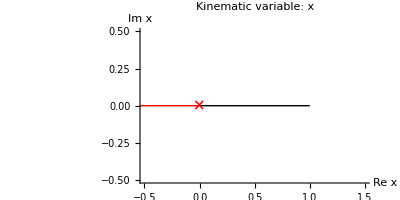

SeaSyde: Moving from the point x=0. to x=1., along the line x=1. tInt

SeaSyde: The new point is: x=0.5

SeaSyde: The new point is: x=0.75

SeaSyde: I arrived at x=1.. The error estimate is: 6.18754×10^-14.
Use Solution[] or SolutionValue[] to access the solution, or CreteGraph to plot it.

```mathematica
TransportVariable[x,1]
```

For convenience, we stored the value of the Master Integrals in x = 1, y = 1 in "bc_numerical.m" and used them as numerical boundary conditions .

Now we can move to the physical region. The physical region, in terms of the variables x and y, is given by x≤0 and 0≤y≤-x, in our conventions. We can perform the analytic continuation of the solution inside the physical region by moving one variable at the time

SeaSyde: Moving following these points: {1.,1.-0.5 ⅈ,-5.-0.5 ⅈ,-5.}, avoiding singularities. Here you can see the path in the complex plane for the kinematic variable x

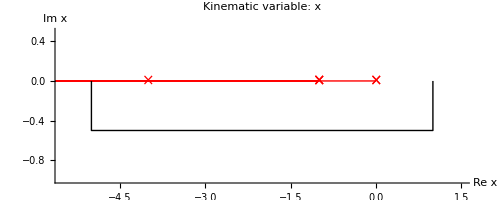

SeaSyde: Moving from the point x=1. to x=1.-0.5 ⅈ, along the line x=1.-(0.+0.5 ⅈ) tInt

SeaSyde: The new point is: x=1.-0.5 ⅈ

SeaSyde: Moving from the point x=1.-0.5 ⅈ to x=-5.-0.5 ⅈ, along the line x=(1.-0.5 ⅈ)-6. tInt

SeaSyde: The new point is: x=0.440983-0.5 ⅈ

SeaSyde: The new point is: x=0.107642-0.5 ⅈ

SeaSyde: The new point is: x=-0.148086-0.5 ⅈ

SeaSyde: The new point is: x=-0.40882-0.5 ⅈ

SeaSyde: The new point is: x=-0.73175-0.5 ⅈ

SeaSyde: The new point is: x=-1.01546-0.5 ⅈ

SeaSyde: The new point is: x=-1.26558-0.5 ⅈ

SeaSyde: The new point is: x=-1.54865-0.5 ⅈ

SeaSyde: The new point is: x=-1.91981-0.5 ⅈ

SeaSyde: The new point is: x=-2.44327-0.5 ⅈ

SeaSyde: The new point is: x=-3.20698-0.5 ⅈ

SeaSyde: The new point is: x=-3.67572-0.5 ⅈ

SeaSyde: The new point is: x=-3.9737-0.5 ⅈ

SeaSyde: The new point is: x=-4.22404-0.5 ⅈ

SeaSyde: The new point is: x=-4.49799-0.5 ⅈ

SeaSyde: The new point is: x=-4.85084-0.5 ⅈ

SeaSyde: Moving from the point x=-5.-0.5 ⅈ to x=-5., along the line x=(-5.-0.5 ⅈ)+(0.+0.5 ⅈ) tInt

SeaSyde: I arrived at x=-5.. The error estimate is: 6.18754×10^-14.
Use Solution[] or SolutionValue[] to access the solution, or CreteGraph to plot it.

SeaSyde: Moving following these points: {1.,3.}, avoiding singularities. Here you can see the path in the complex plane for the kinematic variable y

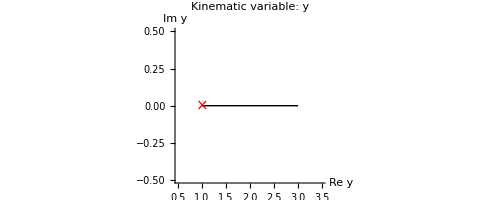

SeaSyde: Moving from the point y=1. to y=3., along the line y=1.+2. tInt

SeaSyde: The new point is: y=1.5

SeaSyde: The new point is: y=1.75

SeaSyde: The new point is: y=2.125

SeaSyde: The new point is: y=2.6875

SeaSyde: I arrived at y=3.. The error estimate is: 6.18754×10^-14.
Use Solution[] or SolutionValue[] to access the solution, or CreteGraph to plot it.

```mathematica
TransportBoundaryConditions[{-5,3}]
```

We can access the solution using

```mathematica
SolutionValue[][[36]]//N
```

(-2.33653×10^-17+2.54754×10^-17 ⅈ) ϵ-(0.0670751+0.0453531 ⅈ) ϵ^2+(0.0733547-0.192686 ⅈ) ϵ^3+(0.253813+0.404438 ⅈ) ϵ^4

### Complex masses

The variables x and y that appear in the equations are adimensional variables defined as follow
x=-s/μ^2=-(p_1+p_2)^2/μ^2,     y=-t/μ^2=-(p_1+p_3)^2/μ^2=-x/2(1-cos θ)
where M is the mass of the exchanged boson,  s and t are the Mandelstam invariants, p_1 and p_2 the incoming momenta,  p_3one of the outgoing momentum, and θ is the scattering angle in the CM frame. When working in the complex mass scheme, the masses of unstable particles are written as μ^2=m^2- ⅈ Γ m), where m and Γ are two real parameters which indicate the mass and the decay rate of the particle, respectively. We see from the equation above that the dimensionless variables x and y get complex-valued, however with the analytic continuation algorithm implemented in SeaSyde, we are still able to obtain a result.

Let us consider for example:
m=m_W=80.358 GeV
Γ=Γ_W=2.084 GeV
μ^2=m^2-ⅈmΓ
√s=100 GeV
cos θ=0.5

Hence
x= -1.54757-0.0401345 ⅈ
y= 0.386892+0.0100336 ⅈ

SeaSyde: File EquationsAndBC/NeutralCurrentDrellYan/bc_numerical.m has been correctly read.

SeaSyde: There are 2 kinematics variables {x,y}

SeaSyde: The Feynman prescriptions for the variables are {-ⅈ δ,ⅈ δ}

SeaSyde: There are 36 Master Integrals

SeaSyde: The boundary conditions are imposed in {x==1.,y==1.}

SeaSyde: The boundary conditions are given as precise value of the solution.

SeaSyde: There are 72 equations and 36 boundary conditions

SeaSyde: The possible singularities for the kinematics variables {x,y} are respectively {{0.,-1.,-4.,-1. y,-4.+4./y,-(4. y^2)/(1.+y)^2},{-1. x,0.,4./(4.+x),-(1. (2. √(-1. x)+x))/(4.+x),(2. √(-1. x)-1. x)/(4.+x),1.}}

SeaSyde: The system of differential equation has been set and expanded in ϵ

SeaSyde: Moving following these points: {1.,1.-0.5 ⅈ,-1.54757-0.5 ⅈ,-1.54757-0.0401345 ⅈ}, avoiding singularities. Here you can see the path in the complex plane for the kinematic variable x

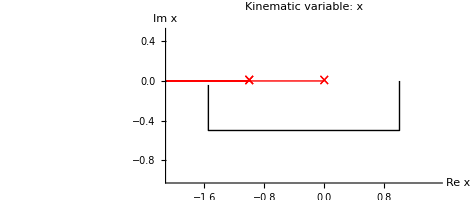

SeaSyde: Moving from the point x=1. to x=1.-0.5 ⅈ, along the line x=1.-(0.+0.5 ⅈ) tInt

SeaSyde: The new point is: x=1.-0.5 ⅈ

SeaSyde: Moving from the point x=1.-0.5 ⅈ to x=-1.54757-0.5 ⅈ, along the line x=(1.-0.5 ⅈ)-2.54757 tInt

SeaSyde: The new point is: x=0.440983-0.5 ⅈ

SeaSyde: The new point is: x=0.107642-0.5 ⅈ

SeaSyde: The new point is: x=-0.148086-0.5 ⅈ

SeaSyde: The new point is: x=-0.40882-0.5 ⅈ

SeaSyde: The new point is: x=-0.73175-0.5 ⅈ

SeaSyde: The new point is: x=-1.01546-0.5 ⅈ

SeaSyde: The new point is: x=-1.26558-0.5 ⅈ

SeaSyde: Moving from the point x=-1.54757-0.5 ⅈ to x=-1.54757-0.0401345 ⅈ, along the line x=(-1.54757-0.5 ⅈ)+(0.+0.459866 ⅈ) tInt

SeaSyde: The new point is: x=-1.54757-0.129246 ⅈ

SeaSyde: I arrived at x=-1.54757-0.0401345 ⅈ. The error estimate is: 9.28469×10^-12.
Use Solution[] or SolutionValue[] to access the solution, or CreteGraph to plot it.

SeaSyde: Moving following these points: {1.,0.386892+0.0100336 ⅈ}, avoiding singularities. Here you can see the path in the complex plane for the kinematic variable y

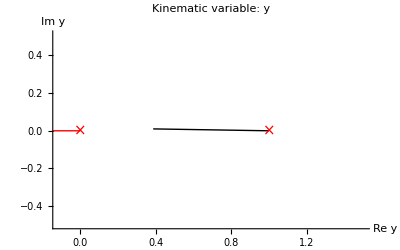

SeaSyde: Moving from the point y=1. to y=0.386892+0.0100336 ⅈ, along the line y=1.-(0.613108-0.0100336 ⅈ) tInt

SeaSyde: The new point is: y=0.725517+0.00449195 ⅈ

SeaSyde: The new point is: y=0.588276+0.00673792 ⅈ

SeaSyde: I arrived at y=0.386892+0.0100336 ⅈ. The error estimate is: 9.28469×10^-12.
Use Solution[] or SolutionValue[] to access the solution, or CreteGraph to plot it.

(1.91716×10^-17+1.68275×10^-17 ⅈ) ϵ-(0.0181991+0.0000865255 ⅈ) ϵ^2-(0.0337195+0.0557183 ⅈ) ϵ^3+(0.14896+0.0970518 ⅈ) ϵ^4

```mathematica
NewPointBC={1,1};
BoundaryConditionsNumerical=ReadFrom[dir<>"bc_numerical.m"];
SetSystemOfDifferentialEquation[FullSystemOfEquations,BoundaryConditionsNumerical,MasterIntegrals,{x-I δ,y+I δ},NewPointBC]

TransportBoundaryConditions[{-1.54757-0.0401345 ⅈ,0.386892+0.0100336 ⅈ}]

SolutionValue[][[36]]//N
```